```mathematica
en=1000;(*系综*)
```

```mathematica
dt=0.01;t=5;(*时间*)
(*参数*)
len=IntegerPart[t/dt];
x0=1;
mu=Table[Sin[i*dt],{i,1,len}];
sigma=Table[10,{i,1,len}];
```

```mathematica
tlist=Table[dt*n,{n,1,len}];(*时间标号*)
Xlist=Table[0,len];(*x(t)标号*)
```

```mathematica
Table[{
x=x0;xlist=Table[0,len];(*初始化x*)
list=RandomVariate[NormalDistribution[0,dt],len];(*产生随机参数*)
Table[{x=x+mu[[n]]*dt+sigma[[n]]*list[[n]],xlist[[n]]=x},{n,1,len}];(*迭代*)
Table[Xlist[[i]]=Xlist[[i]]+xlist[[i]],{i,1,len}];(*收集当前系统的解*)
},en];
Xlist=Xlist/en;
```

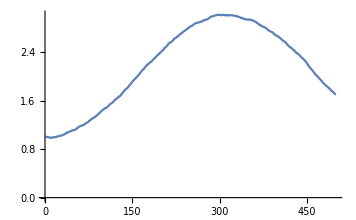

```mathematica
Xlist//ListLinePlot
```